# Introduction to Stochastic Processes

Collections of random variables are useful models of many random processes

Colin Nancarrow, Jun. 24,  2018

A stochastic process is a collection of random variables indexed by some set. For example, a random variable is the simplest kind of stochastic process: it’s just a random variable indexed by one object, or the singleton set. The most common sets used to index random variables in stochastic processes are:
	1. The singleton set for a single random variable 
	2. The natural numbers for indexing successive trials
	3. The real numbers for parameterizing some randomly-evolving quantity
Stochastic processes are very common in our world. Examples include percolation (the study of the motion of a liquid through a porous material) brownian motion (the study of the random motion of large particles subjected to sudden, small shocks) price fluctuations in the stock market, weather data, medical data (e.g. blood pressure, EKG, EEG, temperature) and random walks.

## A random walk

Suppose we have a bug moving in 1 dimension. He takes 1 step each second. With probability p, the step is forward; with probability 1-p the step is backward. Let’s make a plot of the trajectory of such a bug over 100 steps, taking p to be .5 for now:

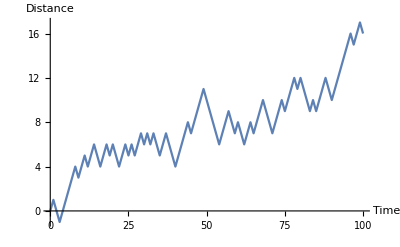

```mathematica
wanderingBug[p_]/;0≤p≤1:=RandomWalkProcess[p]
firstBug = wanderingBug[0.5];
firstBugPath=RandomFunction[RandomWalkProcess[0.5],{0,100}];
ListLinePlot[firstBugPath,AxesLabel->{"Time","Distance"}]
```

Let’s also visualize one hundred paths starting at 0 of the same sort of bug:

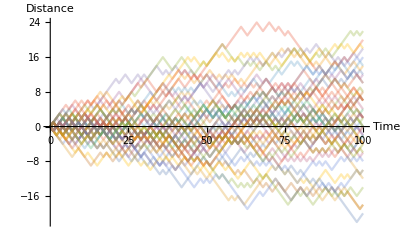

```mathematica
ListLinePlot[RandomFunction[firstBug,{0,100},50],PlotStyle->Opacity[0.3],AxesLabel->{"Time","Distance"}]
```

The bugs’ paths seem to spread out quite a bit around 0, but as a distribution they remain basically symmetrical about 0. Let’s check out how the distributions of paths evolve with changing p by using the Manipulate function:

```mathematica
Manipulate[ListLinePlot[RandomFunction[wanderingBug[p],{0,100},50],AxesLabel->{"Time","Distance"},PlotStyle->Opacity[0.3]],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

As we ought to expect, as p increases the bug spends more time at positive distance from the origin. Interestingly, the spread of the paths tightens up as p gets further away from 0.5. We should definitely have expected this for p = 0 or 1, since this means the bug “almost always” walks backward or forward respectively. Can we argue for the nondegenerate case that this should happen? Sure, with some extra math.

There is a distribution called the BinomialDistribution[n,p] which is a discrete probability distribution which will tell you the probability of having k successes in a game with n trials of which the success probability is p. This relates to our bug by mapping “successes” onto “moves forward” and “failures” onto “moves backward;” hence, if we have k moves forward in t steps, the bug will have moved forward k times and backward t-k times for a total motion of 2k-t. Hence our distribution for the bug’s position at time t is

```mathematica
𝒟=TransformedDistribution[2k-t,k\[Distributed]BinomialDistribution[t,p]]
```

TransformedDistribution[2 x-t,x\[Distributed]BinomialDistribution[t,p]]

```mathematica
PDF[𝒟]
```

Function[x,Piecewise[{{(1-p)^(1/2 (-x-t)+t) p^((x+t)/2) Binomial[t,(x+t)/2], x+t≥0&&x-t≤0}, {0, True}}],Listable]

The conditional bit is a bit funky. Let’s plot just the nonconditional bit and see if it’s basically what we expect, handling by cases p=0 and p=1.

```mathematica
bugDist[p_][t_][x_]/;0≤p≤1:=Piecewise[({{(1-p)^(1/2 (-x-t)+t) p^((x+t)/2) Binomial[t, (x+t)/2], 0<p<1&&-t≤x≤t}, {KroneckerDelta[x,t], p==1}, {KroneckerDelta[x,-t], p==0}})]
```

```mathematica
steps=20;
Manipulate[DiscretePlot3D[bugDist[p][t][x],{t,0,steps},{x,-steps,steps},AxesLabel->{"Steps taken","Bug location","Probability"},ExtentSize->Full,ColorFunction->Hue],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

This big Manipulate graphic won’t load very smoothly past about 20 steps taken, but we can still compare it with the paths of 50 bugs taking 20 steps, which we produce again here for convenience so you can compare with the probability distributions above:

```mathematica
Manipulate[ListLinePlot[RandomFunction[wanderingBug[p],{0,20},50],AxesLabel->{"Time","Distance"},PlotStyle->Opacity[0.3]],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

Let’s also collect histograms on bug movement to check with our result: here’s a manipulatable histogram on the final positions of 500 bugs having taken 20 steps:

```mathematica
makeBugPaths[p_]:=RandomFunction[wanderingBug[p],{0,100},500]["PathFunction",All]
Manipulate[Histogram[#[20]&/@makeBugPaths[p],{-21,21,1}],{{p,0.5,"p"},0,1,.1,Appearance->"Labeled"}]
```

## Section Header

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)